amplitude

707

zero - 1200Hz

58

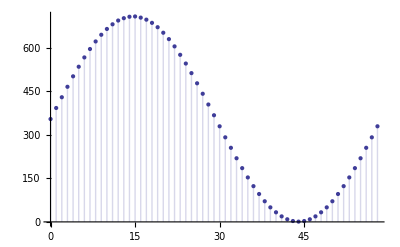

one - 2200Hz

31

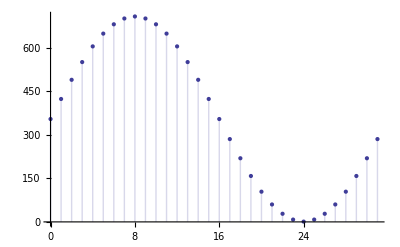

zero - 1200Hz

(354.
392.
429.
465.
501.
534.
566.
595.
621.
644.
664.
680.
693.
701.
706.
707.
703.
696.
685.
670.
651.
629.
604.
575.
545.
512.
477.
441.
404.
367.
329.
291.
255.
219.
185.
153.
123.
96.
71.
50.
33.
19.
9.
3.
1.
3.
9.
19.
33.
50.
71.
96.
123.
153.
185.
219.
255.
291.
329.)

one - 2200Hz

(354.
423.
489.
550.
604.
648.
680.
700.
707.
700.
680.
648.
604.
550.
489.
423.
354.
285.
219.
158.
104.
60.
28.
8.
1.
8.
28.
60.
104.
158.
219.
285.)

```mathematica
Clear["Global`*"]
samples:=32
amplitude:=707
halfAmplitude:=((amplitude-1)/2)
period1:=(2π)/samples
samplesCount1:=Round[(2π)/period1]-1
period0:=1200/2200 period1
samplesCount0:=Floor[(2π)/period0]
f0[x_]:=Round[1+halfAmplitude(1+Sin[period0*x])]
f1[x_]:=Round[1+halfAmplitude(1+Sin[period1*x])]

"amplitude"
Round[amplitude]
"zero - 1200Hz"
samplesCount0
DiscretePlot[f0[x],{x,0,samplesCount0},PlotRange->{{0,samplesCount0},{0,amplitude}}]
"one - 2200Hz"
samplesCount1
DiscretePlot[f1[x],{x,0,samplesCount1},PlotRange->{{0,samplesCount1},{0,amplitude}}]
"zero - 1200Hz"
MatrixForm[Table[N[f0[x]],{x,0,samplesCount0,1}]]
"one - 2200Hz"
MatrixForm[Table[N[f1[x]],{x,0,samplesCount1,1}]]
```